### Definitions

```mathematica
CleanUpData[AList_]:=Reap[
Do[If[AList[[i,1]]≠0.0,Sow[AList[[i]]]],{i,1,Length[AList]}]
][[2,1]];

tickFormat[xmin_,xmax_,digits_,divisions_: 10]:=Function[tickNumber,{tickNumber,PaddedForm[Round[tickNumber,0.01],{Max@(Length@IntegerDigits@IntegerPart[#]&/@(10^digits {xmin,xmax})),digits}]}]/@FindDivisions[{xmin,xmax},divisions];

lineStyle={Thick,Red,Dashed};
StickSpectrum[input_]:=(
Join[{Directive[lineStyle]},Map[Line[{{#[[1]],0.0},{#[[1]],#[[2]]}}]&,input]]
)
```

```mathematica
(*Returns, {{Freqs,Amplitudes}} Given {{Times (atomic units),Signal}}*)
```

```mathematica
Decay[input_]:=(
gam=Log[10^(-3.0)]/(-Length[input]);
dseries=Table[Exp[-(gam*(i-1))],{i,1,Length[input]}];
Return[input*dseries];
)
IsoFourierWithUnits[Path_,Zoom_:1/70.]:=(
xdata=CleanUpData[Import[Path<>"S10_Pol.csv","Table"]];
ydata=CleanUpData[Import[Path<>"S20_Pol.csv","Table"]];
zdata=CleanUpData[Import[Path<>"S30_Pol.csv","Table"]];
xdat=xdata[[All,2]]-Mean[xdata[[All,2]]];
ydat=ydata[[All,3]]-Mean[ydata[[All,3]]];
zdat=zdata[[All,4]]-Mean[zdata[[All,4]]];
n=Min[Map[Length,{xdat,ydat,zdat}]];
n=If[Mod[n,2]==1,n-1,n];
xdat=Decay[xdat[[1;;n]]];
ydat=Decay[ydat[[1;;n]]];
zdat=Decay[zdat[[1;;n]]];
dt=(xdata[[3,1]]-xdata[[2,1]]);
isodat =MapThread[(#1+#2+#3)&,{xdat,ydat,zdat}];
fx = Abs[Fourier[isodat,FourierParameters->{1,Zoom}]];
Freqs=π*(27.2113*2.0/dt)*Zoom*Range[Length[xdat]/2]/Length[xdat];
Spec=MapThread[{#1,#1*#2}&,{Freqs,fx[[1;;n/2]]}];
Return[Spec]
)

FourierWithUnits[dataa_,Col_:2,Zoom_:1/2.,dcy_:True]:=(
data=dataa[[All,Col]]-Mean[dataa[[All,Col]]];
If[dcy,data=Decay[data]];
dt=(dataa[[3,1]]-dataa[[2,1]]);
n=Length[data];
n=If[Mod[n,2]==1,n-1,n];
f = Fourier[data,FourierParameters->{1,Zoom}];
f = Abs[f];
Freqs=π*(27.2113*2.0/dt)*Zoom*Range[Length[data]/2]/Length[data];
Spec=MapThread[{#1,#1*#2}&,{Freqs,f[[1;;n/2]]}];
Return[Spec]
)
```

```mathematica
FourierNoUnits[dataa_,Zoomm_:1/2.]:=(
data=dataa-Mean[dataa];
n=Length[data];
n=If[Mod[n,2]==1,n-1,n];
f = Fourier[data,FourierParameters->{1,Zoomm}];
f =Sqrt[Abs[f]];
Return[f[[1;;n/2]]]
)
(*Just Returns the Freq*)
FourierFreqs[data_,Zoomm_:1/2.]:=(
dt=(data[[3]]-data[[2]]);
n=Length[data];
n=If[Mod[n,2]==1,n-1,n];
Freqs=π*(27.2113*2.0/dt)*Zoomm*Range[Length[data]/2]/Length[data];
Return[Freqs]
)
```

```mathematica
(*Window is in input Time units and a cos-window is used*)
Clear[SpectroGram];
SpectroGram[TimeSeries_,WinLength_,DataCol_:2,Zoom_:1/5.]:=(
over=Round[WinLength/4.];
window=N[Table[1-(0.54+0.46 Cos[2 Pi i/WinLength]),{i,1,WinLength}]];
JustData=Map[#[[DataCol]]&,TimeSeries];
JustTimes=TimeSeries[[1;;WinLength,1]] ;
Print["TMax: (au) ",JustTimes[[-1]]];
PData=Partition[JustData,WinLength,over];
EachTimes=Partition[TimeSeries[[All,1]],WinLength,over];
FLabels=FourierFreqs[JustTimes,Zoom];
Print["FMax (eV):",FLabels[[-1]]];
Return[{Map[FourierNoUnits[#,Zoom]&,PData],FLabels,Table[EachTimes[[i,Length[PData[[1]]]/2]]*0.0241888,{i,1,Length[PData]}]}]
)
```

### Debugging tdscf_pyscf

```mathematica
DatRPA=CleanUpData[Import["/Users/johnparkhill/tdscf_pyscf/log.dat","Table"]];
```

```mathematica
DatRPA[[1;;2,;;]]
```

{{0.02,0.,0.,0.,-2.17191,(2+0j)},{0.04,0.,0.,0.,-2.17191,(2+0j)}}

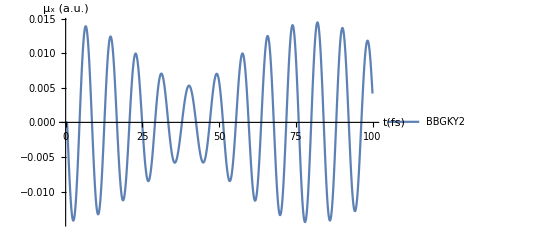

```mathematica
ListPlot[{DatRPA[[1;;,{1,4}]]},PlotRange->{{0,100},All},Joined->True,PlotStyle->{Thick,Dotted},PlotLegends->{"BBGKY2","TDHF","EE2"},AxesLabel->{Style["t(fs)",19],Style["μ_x (a.u.)",19]},LabelStyle->19]
```

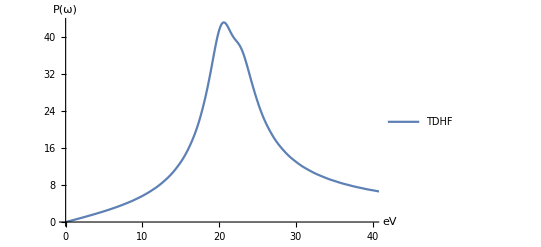

```mathematica
ListPlot[{Map[{#[[1]],#[[2]]*0.5}&,FourierWithUnits[DatRPA,4,1/60.]]},Joined->True,PlotRange->{{0,40},All},PlotLegends->{"TDHF"},AxesLabel->{Style["eV",19],Style["P(ω)",23]},LabelStyle->19]
```